## Probabilità dallo stato attuale alternativa cos/sin

```mathematica
L=80;
hx=0.8;
hz=0.01;
δt=80;
chain={Table[3π/2,{i,1,L}]};
chainplus=Table[3π/2,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
θ[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 Sin[θ[i-1]]Sin[θ[i]]+0.5 Sin[θ[i+1]]Sin[θ[i]]+hx Cos[θ[i]]+hz Sin[θ[i]]);
energyi[i_]:=-(0.5 Sin[θ[i-1]]Sin[θi]+0.5 Sin[θ[i+1]]Sin[θi]+hx Cos[θi]+hz Sin[θi]);
min[i_]:=MinValue[{energyi[i],θi≤2π,θi≥0},zi];
𝒟[i_]:=ProbabilityDistribution[1/(1+ⅇ^((energyi[i]-energy[i])δt)),{θi,0,2π},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

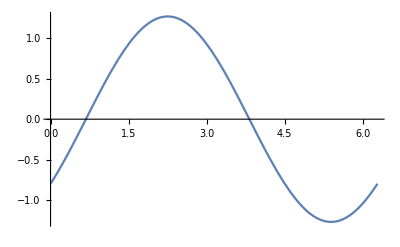

```mathematica
Plot[energyi[3],{θi,0,2π}]
```

Piecewise[{{0.736217/(1+ⅇ^(80 (0.99-0.8 Cos[θi]+0.99 Sin[θi]))), 0<θi<2 π}, {0, True}}]

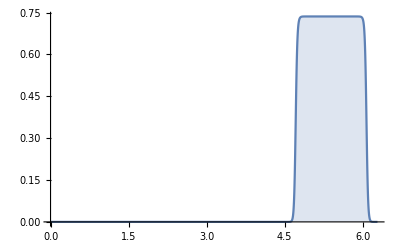

```mathematica
PDF[𝒟[3],θi]
Plot[%,{θi,0,2π},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

5.63317

```mathematica
chain={Table[3π/2,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,150}]
```

```mathematica
MatrixPlot[Transpose[Sin[chain]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
0.01
```

-Graphics-

```mathematica
0.02
```

-Graphics-

```mathematica
0.05
```

-Graphics-

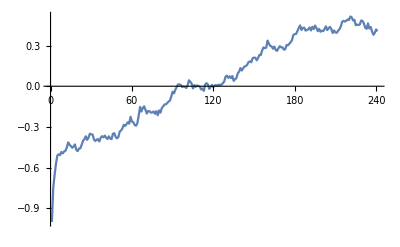

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

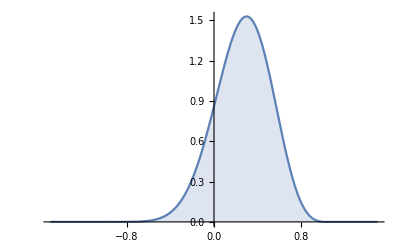

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

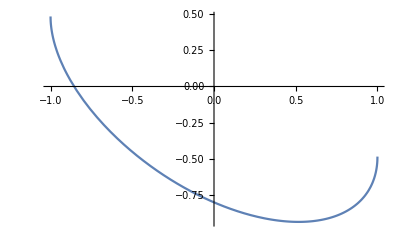

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

```mathematica
chain={Table[-1,{i,1,L}]};
```

Piecewise[{{1.2667/(1+ⅇ^(80 (0.99+0.99 zi-0.8 √(1-zi^2)))), -1<zi<1}, {0, True}}]

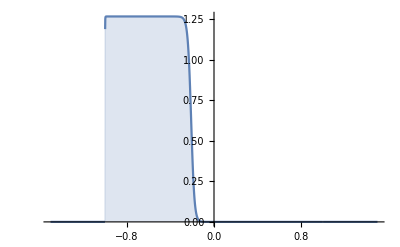

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```